```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/kidinnu/Yandex.Disk/Documents/Disciplines/matlab/ODE-OrbitalMotion

```mathematica
{1,(2*100)/(6371.0+500),100^2/(6371.0+500)^2}
{Total[%],Total[%[[1;;2]]]}
(%[[1]]-%[[2]])/(%[[1]])*100.0
```

{1,0.0291078,0.000211817}

{1.02932,1.02911}

0.0205783

```mathematica
Series[(1+2 x/r)^(-3/2),{x,0,1}]
```

1-(3 x)/r+O[x]^2

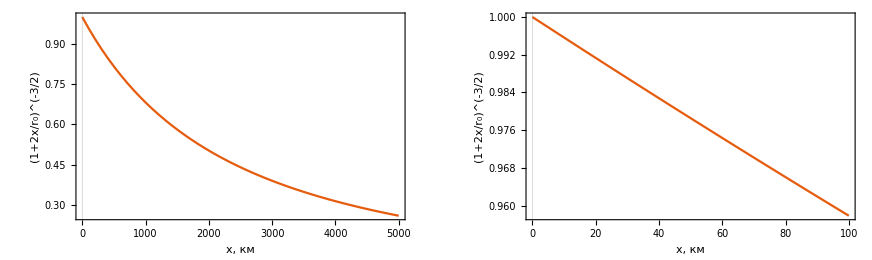

f.pdf

```mathematica
GraphicsRow[{Plot[(1+2 x/(6370+500))^(-3/2),{x,0,5000},PlotTheme->"Scientific",FrameLabel->{"x, км","(1+2x/r_0)^(-3/2)"}],
Plot[(1+2 x/(6370+500))^(-3/2),{x,0,100},PlotTheme->"Scientific",FrameLabel->{"x, км","(1+2x/r_0)^(-3/2)"}]}]
Export["f.pdf",%]
```

```mathematica
2*π √(1/(3.986 10^14)(6371000+200000)^3)
```

5301.01

```mathematica
√((3.986 10^14)/(6371000+200000)^3)
```

0.00118528